# Box diagrams

## Load FeynCalc

```mathematica
description="Learning FeynCalc through examples.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts","FeynHelpers"};
<<FeynCalc`
$FAVerbose=0;

FCCheckVersion[9,3,1];
(FAPatch[PatchModelsOnly->True];)
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

Successfully patched FeynArts.

```mathematica
$KeepLogDivergentScalelessIntegrals = True;
```

```mathematica
$ToolsRoot=NotebookDirectory[];
AppendTo[$Path,FileNameJoin[{$ToolsRoot,"Include"}]];
<<Tools`
<<PrettyNotation`
```

Get::noopen: Cannot open Tools`.

$Failed

Get::noopen: Cannot open PrettyNotation`.

$Failed

```mathematica
MakeBoxes[p1,TraditionalForm]:=SubscriptBox["p","1"];
MakeBoxes[p2,TraditionalForm]:=SubscriptBox["p","2"];
MakeBoxes[k1,TraditionalForm]:=SubscriptBox["k","1"];
MakeBoxes[k2,TraditionalForm]:=SubscriptBox["k","2"];
MakeBoxes[m1,TraditionalForm]:=SubscriptBox["m","1"];
MakeBoxes[m2,TraditionalForm]:=SubscriptBox["m","2"];
MakeBoxes[m3,TraditionalForm]:=SubscriptBox["m","3"];
MakeBoxes[x0,TraditionalForm]:=SubscriptBox["x","0"];
MakeBoxes[x1,TraditionalForm]:=SubscriptBox["x","1"];
MakeBoxes[x2,TraditionalForm]:=SubscriptBox["x","2"];
MakeBoxes[xγ,TraditionalForm]:=SubscriptBox["x","γ"];
MakeBoxes[u1,TraditionalForm]:=SubscriptBox["u","1"];
MakeBoxes[u2,TraditionalForm]:=SubscriptBox["u","2"];
MakeBoxes[uγ,TraditionalForm]:=SubscriptBox["u","γ"];
MakeBoxes[z1,TraditionalForm]:=SubscriptBox["z","1"];
MakeBoxes[z2,TraditionalForm]:=SubscriptBox["z","2"];
MakeBoxes[zγ,TraditionalForm]:=SubscriptBox["z","γ"];
MakeBoxes[a1,TraditionalForm]:=SubscriptBox["a","1"];
MakeBoxes[a2,TraditionalForm]:=SubscriptBox["a","2"];
MakeBoxes[aγ,TraditionalForm]:=SubscriptBox["a","γ"];
MakeBoxes[β1,TraditionalForm]:=SubscriptBox["β","1"];
MakeBoxes[β2,TraditionalForm]:=SubscriptBox["β","2"];
MakeBoxes[xp,TraditionalForm]:=SuperscriptBox["x","+"];
MakeBoxes[xm,TraditionalForm]:=SuperscriptBox["x","-"];
MakeBoxes[λs,TraditionalForm]:=SubscriptBox["λ","s"];
MakeBoxes[λQ,TraditionalForm]:=SubscriptBox["λ","Q"];
MakeBoxes[c1,TraditionalForm]:=SubscriptBox["c","1"];
MakeBoxes[c2,TraditionalForm]:=SubscriptBox["c","2"];
```

## Find amplitudes

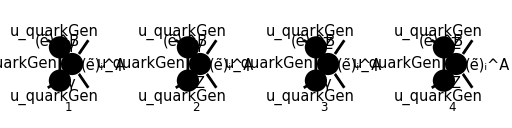

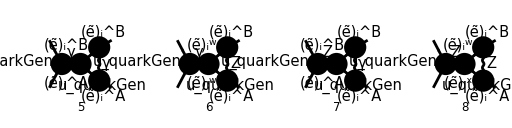

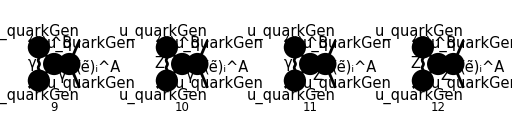

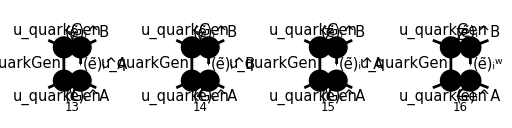

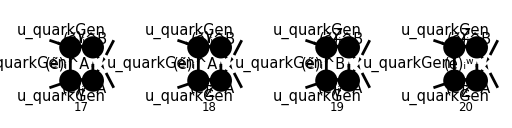

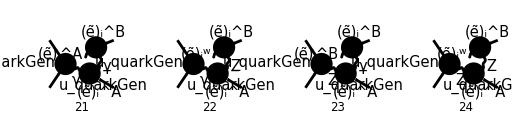

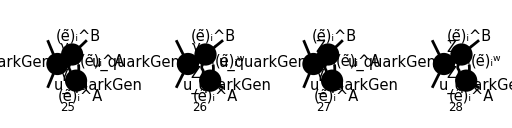

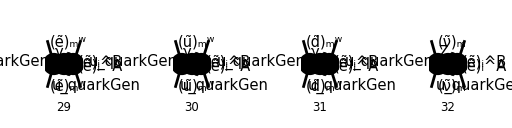

```mathematica
diagsVirt[0]=InsertFields[
CreateTopologies[1,2->2,
ExcludeTopologies->{Tadpoles,SelfEnergies}],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],(*Higgs*)
S[13,14],(*Squarks*)
V[3],(*Z, W*)
F[11|12](*Electroweakinos*)
}
];
Paint[
diagsVirt[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

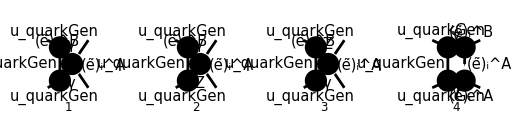

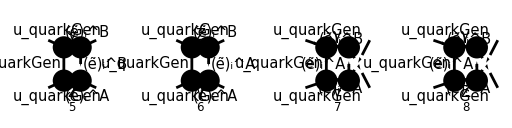

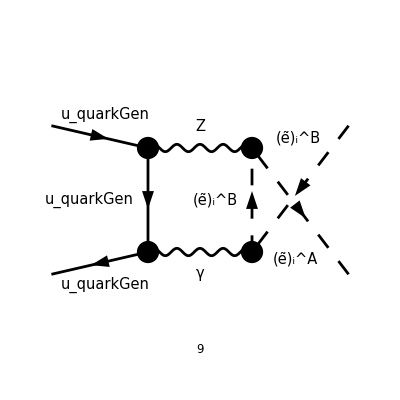

```mathematica
diagsVirt[1]=DiagramExtract[diagsVirt[0],{1,2,3,13,14,15,17,18,19}];
Paint[
diagsVirt[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,m1,m2];
```

```mathematica
FAD[k,k+p1,k+p1+p2,{k+k1,m}]
%//TID[#,k,ToPaVe->True]&
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&
```

1/(k^2.(k+p_1)^2.(k+p_1+p_2)^2.((k+k_1)^2-m^2))

ⅈ π^2 D_0(0,0,m_1^2,3 m_1^2+s-t-u,s,2 m_1^2-t,0,0,0,m^2)

-(ⅈ KK(159))/ε_IR^2+(ⅈ KK(163))/ε_IR-1/4 ⅈ KK(176)

```mathematica
KK[159]
```

π^2/(KK(158) s)

```mathematica
SpinorVBarD[p2].GSD[k+k1-k2].GSD[k+p1].GSD[k+2k1].SpinorUD[p1]
%/.{k->k+x p1+y(p1+p2)+z k1}//DiracGammaExpand
%//ReplaceAll[#,{
GSD[x p1]->x GSD[p1],
GSD[y p1]->y GSD[p1],
GSD[x p2]->x GSD[p2],
GSD[y p2]->y GSD[p2],
GSD[x k1]->x GSD[k1],
GSD[y k1]->y GSD[k1],
GSD[x k2]->x GSD[k2],
GSD[y k2]->y GSD[k2]
}]&
%//DiracSimplify//Simplify
```

v̄(p_2).(γ·(k+k_1-k_2)).(γ·(k+p_1)).(γ·(k+2 k_1)).u(p_1)

(φ(-p_2)).(γ·k+γ·k_1-γ·k_2+γ·k_1 z+γ·p_1 x+γ·p_1 y+γ·p_2 y).(γ·k+γ·k_1 z+γ·p_1+γ·p_1 x+γ·p_1 y+γ·p_2 y).(γ·k+2 γ·k_1+γ·k_1 z+γ·p_1 x+γ·p_1 y+γ·p_2 y).(φ(p_1))

(φ(-p_2)).(γ·k+γ·k_1-γ·k_2+γ·k_1 z+γ·p_1 x+γ·p_1 y+γ·p_2 y).(γ·k+γ·k_1 z+γ·p_1+γ·p_1 x+γ·p_1 y+γ·p_2 y).(γ·k+2 γ·k_1+γ·k_1 z+γ·p_1 x+γ·p_1 y+γ·p_2 y).(φ(p_1))

2 (φ(-p_2)).(γ·k_2).(φ(p_1)) m_1^2-4 (φ(-p_2)).(γ·p_1 x).(φ(p_1)) m_1^2-4 (φ(-p_2)).(γ·p_1 y).(φ(p_1)) m_1^2-4 (φ(-p_2)).(γ·p_2 y).(φ(p_1)) m_1^2-4 (φ(-p_2)).(γ·k_1 z).(φ(p_1)) m_1^2-2 t (φ(-p_2)).(γ·k_2).(φ(p_1))+2 t (φ(-p_2)).(γ·p_1 x).(φ(p_1))+2 t (φ(-p_2)).(γ·p_1 y).(φ(p_1))+2 t (φ(-p_2)).(γ·p_2 y).(φ(p_1))+2 t (φ(-p_2)).(γ·k_1 z).(φ(p_1))+2 (φ(-p_2)).(γ·k).(γ·p_1 x).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·k).(γ·p_1 x).(γ·(p_1 y+p_2 y+k_1 z)).(φ(p_1))+2 (φ(-p_2)).(γ·k).(γ·p_1 y).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·k).(γ·p_1 y).(γ·(p_1 x+p_2 y+k_1 z)).(φ(p_1))+2 (φ(-p_2)).(γ·k).(γ·p_2 y).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·k).(γ·p_2 y).(γ·(p_1 x+p_1 y+k_1 z)).(φ(p_1))+2 (φ(-p_2)).(γ·k).(γ·k_1 z).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·k).(γ·k_1 z).(γ·(p_1 x+p_1 y+p_2 y)).(φ(p_1))+(φ(-p_2)).(γ·k_1).(γ·k).(γ·(p_1 x+p_1 y+p_2 y+k_1 z)).(φ(p_1))+(φ(-p_2)).(γ·k_1).(γ·p_1 x).(γ·(k+p_1 y+p_2 y+k_1 z)).(φ(p_1))+(φ(-p_2)).(γ·k_1).(γ·p_1 y).(γ·(k+p_1 x+p_2 y+k_1 z)).(φ(p_1))+(φ(-p_2)).(γ·k_1).(γ·p_2 y).(γ·(k+p_1 x+p_1 y+k_1 z)).(φ(p_1))+(φ(-p_2)).(γ·k_1).(γ·k_1 z).(γ·(k+p_1 x+p_1 y+p_2 y)).(φ(p_1))-2 (φ(-p_2)).(γ·k_2).(γ·k).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·k).(γ·p_1 x).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·k).(γ·p_1 y).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·k).(γ·p_2 y).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·k).(γ·k_1 z).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·p_1 x).(γ·k).(φ(p_1))-2 (φ(-p_2)).(γ·k_2).(γ·p_1 x).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·p_1 x).(γ·p_1 y).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·p_1 x).(γ·p_2 y).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·p_1 x).(γ·k_1 z).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·p_1 y).(γ·k).(φ(p_1))-2 (φ(-p_2)).(γ·k_2).(γ·p_1 y).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·p_1 y).(γ·p_1 x).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·p_1 y).(γ·p_2 y).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·p_1 y).(γ·k_1 z).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·p_2 y).(γ·k).(φ(p_1))-2 (φ(-p_2)).(γ·k_2).(γ·p_2 y).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·p_2 y).(γ·p_1 x).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·p_2 y).(γ·p_1 y).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·p_2 y).(γ·k_1 z).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·k_1 z).(γ·k).(φ(p_1))-2 (φ(-p_2)).(γ·k_2).(γ·k_1 z).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·k_1 z).(γ·p_1 x).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·k_1 z).(γ·p_1 y).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·k_1 z).(γ·p_2 y).(φ(p_1))+2 (φ(-p_2)).(γ·p_1 x).(γ·k).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·p_1 x).(γ·k).(γ·(p_1 y+p_2 y+k_1 z)).(φ(p_1))+2 (φ(-p_2)).(γ·p_1 x).(γ·p_1 y).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·p_1 x).(γ·p_1 y).(γ·(k+p_2 y+k_1 z)).(φ(p_1))+2 (φ(-p_2)).(γ·p_1 x).(γ·p_2 y).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·p_1 x).(γ·p_2 y).(γ·(k+p_1 y+k_1 z)).(φ(p_1))+2 (φ(-p_2)).(γ·p_1 x).(γ·k_1 z).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·p_1 x).(γ·k_1 z).(γ·(k+p_1 y+p_2 y)).(φ(p_1))+2 (φ(-p_2)).(γ·p_1 y).(γ·k).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·p_1 y).(γ·k).(γ·(p_1 x+p_2 y+k_1 z)).(φ(p_1))+2 (φ(-p_2)).(γ·p_1 y).(γ·p_1 x).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·p_1 y).(γ·p_1 x).(γ·(k+p_2 y+k_1 z)).(φ(p_1))+2 (φ(-p_2)).(γ·p_1 y).(γ·p_2 y).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·p_1 y).(γ·p_2 y).(γ·(k+p_1 x+k_1 z)).(φ(p_1))+2 (φ(-p_2)).(γ·p_1 y).(γ·k_1 z).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·p_1 y).(γ·k_1 z).(γ·(k+p_1 x+p_2 y)).(φ(p_1))+2 (φ(-p_2)).(γ·p_2 y).(γ·k).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·p_2 y).(γ·k).(γ·(p_1 x+p_1 y+k_1 z)).(φ(p_1))+2 (φ(-p_2)).(γ·p_2 y).(γ·p_1 x).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·p_2 y).(γ·p_1 x).(γ·(k+p_1 y+k_1 z)).(φ(p_1))+2 (φ(-p_2)).(γ·p_2 y).(γ·p_1 y).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·p_2 y).(γ·p_1 y).(γ·(k+p_1 x+k_1 z)).(φ(p_1))+2 (φ(-p_2)).(γ·p_2 y).(γ·k_1 z).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·p_2 y).(γ·k_1 z).(γ·(k+p_1 x+p_1 y)).(φ(p_1))+2 (φ(-p_2)).(γ·k_1 z).(γ·k).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·k_1 z).(γ·k).(γ·(p_1 x+p_1 y+p_2 y)).(φ(p_1))+2 (φ(-p_2)).(γ·k_1 z).(γ·p_1 x).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·k_1 z).(γ·p_1 x).(γ·(k+p_1 y+p_2 y)).(φ(p_1))+2 (φ(-p_2)).(γ·k_1 z).(γ·p_1 y).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·k_1 z).(γ·p_1 y).(γ·(k+p_1 x+p_2 y)).(φ(p_1))+2 (φ(-p_2)).(γ·k_1 z).(γ·p_2 y).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·k_1 z).(γ·p_2 y).(γ·(k+p_1 x+p_1 y)).(φ(p_1))-(φ(-p_2)).(γ·k_2).(φ(p_1)) k^2+(φ(-p_2)).(γ·p_1 x).(φ(p_1)) k^2+(φ(-p_2)).(γ·p_1 y).(φ(p_1)) k^2+(φ(-p_2)).(γ·p_2 y).(φ(p_1)) k^2+(φ(-p_2)).(γ·k_1 z).(φ(p_1)) k^2-2 (φ(-p_2)).(γ·k_2).(φ(p_1)) (k·p_1)+2 (φ(-p_2)).(γ·p_1 x).(φ(p_1)) (k·p_1)+2 (φ(-p_2)).(γ·p_1 y).(φ(p_1)) (k·p_1)+2 (φ(-p_2)).(γ·p_2 y).(φ(p_1)) (k·p_1)+2 (φ(-p_2)).(γ·k_1 z).(φ(p_1)) (k·p_1)+2 (φ(-p_2)).(γ·p_1 x).(φ(p_1)) (k·p_1 x)+2 (φ(-p_2)).(γ·p_1 y).(φ(p_1)) (k·p_1 y)+2 (φ(-p_2)).(γ·p_2 y).(φ(p_1)) (k·p_2 y)+2 (φ(-p_2)).(γ·k_1 z).(φ(p_1)) (k·k_1 z)-2 (φ(-p_2)).(γ·k_2).(φ(p_1)) (p_1·p_1 x)+2 (φ(-p_2)).(γ·p_1 x).(φ(p_1)) (p_1·p_1 x)+2 (φ(-p_2)).(γ·p_1 y).(φ(p_1)) (p_1·p_1 x)+2 (φ(-p_2)).(γ·p_2 y).(φ(p_1)) (p_1·p_1 x)+2 (φ(-p_2)).(γ·k_1 z).(φ(p_1)) (p_1·p_1 x)-2 (φ(-p_2)).(γ·k_2).(φ(p_1)) (p_1·p_1 y)+2 (φ(-p_2)).(γ·p_1 x).(φ(p_1)) (p_1·p_1 y)+2 (φ(-p_2)).(γ·p_1 y).(φ(p_1)) (p_1·p_1 y)+2 (φ(-p_2)).(γ·p_2 y).(φ(p_1)) (p_1·p_1 y)+2 (φ(-p_2)).(γ·k_1 z).(φ(p_1)) (p_1·p_1 y)-2 (φ(-p_2)).(γ·k_2).(φ(p_1)) (p_1·p_2 y)+2 (φ(-p_2)).(γ·p_1 x).(φ(p_1)) (p_1·p_2 y)+2 (φ(-p_2)).(γ·p_1 y).(φ(p_1)) (p_1·p_2 y)+2 (φ(-p_2)).(γ·p_2 y).(φ(p_1)) (p_1·p_2 y)+2 (φ(-p_2)).(γ·k_1 z).(φ(p_1)) (p_1·p_2 y)-2 (φ(-p_2)).(γ·k_2).(φ(p_1)) (p_1·k_1 z)+2 (φ(-p_2)).(γ·p_1 x).(φ(p_1)) (p_1·k_1 z)+2 (φ(-p_2)).(γ·p_1 y).(φ(p_1)) (p_1·k_1 z)+2 (φ(-p_2)).(γ·p_2 y).(φ(p_1)) (p_1·k_1 z)+2 (φ(-p_2)).(γ·k_1 z).(φ(p_1)) (p_1·k_1 z)-(φ(-p_2)).(γ·k_2).(φ(p_1)) ((p_1 x)^2)+(φ(-p_2)).(γ·p_1 x).(φ(p_1)) ((p_1 x)^2)+(φ(-p_2)).(γ·p_1 y).(φ(p_1)) ((p_1 x)^2)+(φ(-p_2)).(γ·p_2 y).(φ(p_1)) ((p_1 x)^2)+(φ(-p_2)).(γ·k_1 z).(φ(p_1)) ((p_1 x)^2)+2 (φ(-p_2)).(γ·p_1 x).(φ(p_1)) (p_1 x·p_1 y)+2 (φ(-p_2)).(γ·p_1 y).(φ(p_1)) (p_1 x·p_1 y)+2 (φ(-p_2)).(γ·p_1 x).(φ(p_1)) (p_1 x·p_2 y)+2 (φ(-p_2)).(γ·p_2 y).(φ(p_1)) (p_1 x·p_2 y)+2 (φ(-p_2)).(γ·p_1 x).(φ(p_1)) (p_1 x·k_1 z)+2 (φ(-p_2)).(γ·k_1 z).(φ(p_1)) (p_1 x·k_1 z)-(φ(-p_2)).(γ·k_2).(φ(p_1)) ((p_1 y)^2)+(φ(-p_2)).(γ·p_1 x).(φ(p_1)) ((p_1 y)^2)+(φ(-p_2)).(γ·p_1 y).(φ(p_1)) ((p_1 y)^2)+(φ(-p_2)).(γ·p_2 y).(φ(p_1)) ((p_1 y)^2)+(φ(-p_2)).(γ·k_1 z).(φ(p_1)) ((p_1 y)^2)+2 (φ(-p_2)).(γ·p_1 y).(φ(p_1)) (p_1 y·p_2 y)+2 (φ(-p_2)).(γ·p_2 y).(φ(p_1)) (p_1 y·p_2 y)+2 (φ(-p_2)).(γ·p_1 y).(φ(p_1)) (p_1 y·k_1 z)+2 (φ(-p_2)).(γ·k_1 z).(φ(p_1)) (p_1 y·k_1 z)-(φ(-p_2)).(γ·k_2).(φ(p_1)) ((p_2 y)^2)+(φ(-p_2)).(γ·p_1 x).(φ(p_1)) ((p_2 y)^2)+(φ(-p_2)).(γ·p_1 y).(φ(p_1)) ((p_2 y)^2)+(φ(-p_2)).(γ·p_2 y).(φ(p_1)) ((p_2 y)^2)+(φ(-p_2)).(γ·k_1 z).(φ(p_1)) ((p_2 y)^2)+2 (φ(-p_2)).(γ·p_2 y).(φ(p_1)) (p_2 y·k_1 z)+2 (φ(-p_2)).(γ·k_1 z).(φ(p_1)) (p_2 y·k_1 z)-(φ(-p_2)).(γ·k_2).(φ(p_1)) ((k_1 z)^2)+(φ(-p_2)).(γ·p_1 x).(φ(p_1)) ((k_1 z)^2)+(φ(-p_2)).(γ·p_1 y).(φ(p_1)) ((k_1 z)^2)+(φ(-p_2)).(γ·p_2 y).(φ(p_1)) ((k_1 z)^2)+(φ(-p_2)).(γ·k_1 z).(φ(p_1)) ((k_1 z)^2)+(φ(-p_2)).(γ·k).(φ(p_1)) (-4 m_1^2+2 t+k^2+2 (k·p_1)+2 (k·p_1 x)+2 (k·p_1 y)+2 (k·p_2 y)+2 (k·k_1 z)+2 (p_1·p_1 x)+2 (p_1·p_1 y)+2 (p_1·p_2 y)+2 (p_1·k_1 z)+(p_1 x)^2+(p_1 y)^2+(p_2 y)^2+(k_1 z)^2)+(φ(-p_2)).(γ·k_1).(φ(p_1)) (-2 m_1^2+2 t+3 k^2+4 (k·k_1)+2 (k·p_1)+4 (k_1·p_1 x)+4 (k_1·p_1 y)+4 (k_1·p_2 y)+4 (k_1·k_1 z)+2 (p_1·p_1 x)+2 (p_1·p_1 y)+2 (p_1·p_2 y)+2 (p_1·k_1 z)+3 ((p_1 x)^2)+3 ((p_1 y)^2)+3 ((p_2 y)^2)+3 ((k_1 z)^2))